# Determination of α, β by fitting σ_R to ϵ at Q^2= 5.0 (GeV)^2

R^2/τ =A

2/R= B

2R/τ=X

R/τ= L

G_M^2 = G

σ_R = (G_M)^2 [1 + ϵ A + (B + ϵ X)[α1 (ϵ - 1) + α2 (ϵ^2 - 1)] + [B {1 -( 2 R ϵ/(1 + ϵ))} + 2 ϵ (1 + D)] [β1 (ϵ - 1) + β2 (ϵ^2 - 1)] ]

```mathematica
epsdata={0.389,0.538,0.704,0.919}; 
sigmaRdata={0.002888881,0.002805128,0.002835631,0.002889329};
data=Transpose[{epsdata,sigmaRdata}]
A=0.015698739
B=13.392
X=0.210237515
L=0.105118757
G=0.004697112
R=0.149342891

sigmaR=G*(1+(eps*A) +((B+(eps*X))*(alpha1*(eps-1)+alpha2*(eps^2-1)))+(B*(1-((eps*2*R)/(1+eps)))+ 2*eps*(1+L))*(beta1*(eps-1)+beta2*(eps^2-1)))
FindFit[data, {sigmaR},{alpha1,alpha2,beta1,beta2},eps]
```

{{0.389,0.00288888},{0.538,0.00280513},{0.704,0.00283563},{0.919,0.00288933}}

0.0156987

13.392

0.210238

0.105119

0.00469711

0.149343

0.00469711 (1+0.0156987 eps+(13.392+0.210238 eps) (alpha1 (-1+eps)+alpha2 (-1+eps^2))+(beta1 (-1+eps)+beta2 (-1+eps^2)) (2.21024 eps+13.392 (1-(0.298686 eps)/(1+eps))))

{alpha1→101.579,alpha2→-57.4755,beta1→-104.542,beta2→59.2358}

## Y_E and Y_ 3 Determination with Plot

### α values :

```mathematica
alpha1=101.57910805435057
alpha2=-57.47546413061173
alpha0=-(alpha1+alpha2)
```

101.579

-57.4755

-44.1036

### β values :

```mathematica
beta1=-104.54225890950885
beta2=59.23584087245345
beta0=-(beta1+beta2)
```

-104.542

59.2358

45.3064

### Y_E , Y_ 3 & Y_M :

-44.1036+101.579 eps-57.4755 eps^2

45.3064-104.542 eps+59.2358 eps^2

6.696 (-44.1036+101.579 eps-57.4755 eps^2+(45.3064-104.542 eps+59.2358 eps^2) (1-(0.298686 eps)/(1+eps)))

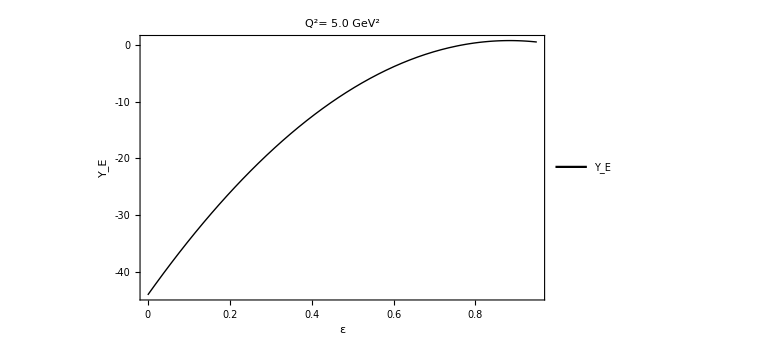

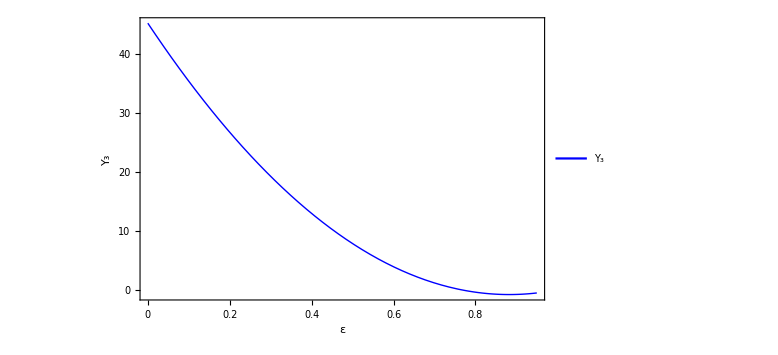

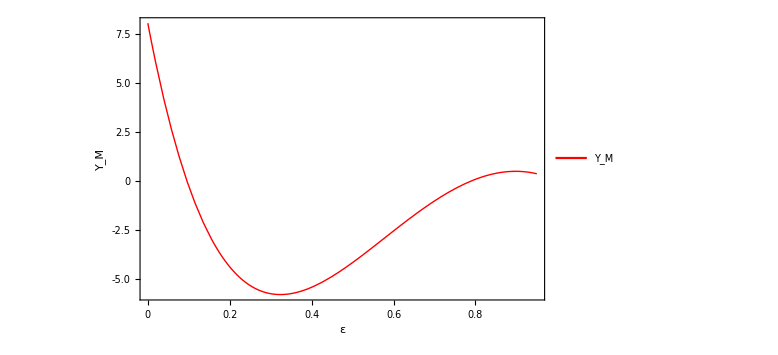

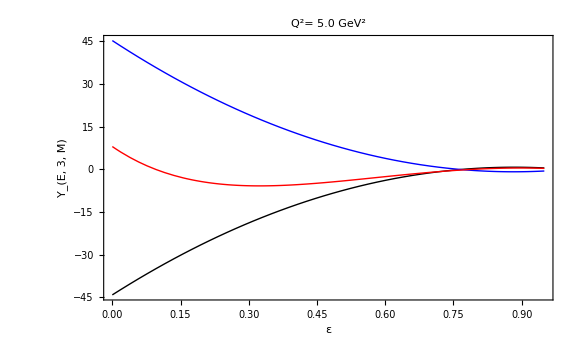

```mathematica
YE=-44.10364392373884+(101.57910805435057*eps)+(-57.47546413061173*eps^2)
Y3=45.306418037055394+(-104.54225890950885*eps)+(59.23584087245345*eps^2)
YM=(YE+(1-R*(2*eps/(1+eps)))*Y3)/R
YEplot=Plot[YE, {eps,0,0.95},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.92,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 5.0 GeV^2",Bold,24], ImageSize-> Large]
Y3plot=Plot[Y3, {eps,0,0.95},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplot=Plot[YM, {eps,0,0.95},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.92,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplot,Y3plot,YMplot, PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,12],ImageSize-> Large]
```

## My Fit

```mathematica
Q2=5
fcmuR=1+(-0.11723721716472688)*Q2+(0.0025226146422440594)*(Q2)^2+(-0.0004347472619650877)*(Q2)^3
fcR=fcmuR/2.7972
```

5

0.422536

0.151057

```mathematica
epsdata={0.389,0.538,0.704,0.919}; 
sigmaRdata={0.002888881,0.002805128,0.002835631,0.002889329};
data=Transpose[{epsdata,sigmaRdata}]
Afc=0.016144132
Bfc=13.20597535
Xfc=0.2132
Lfc=0.17142
Gfc=0.1066
Rfc=0.15105672547076757

sigmaRfc=Gfc*(1+(eps*Afc) +((Bfc+(eps*Xfc))*(alpha1fc*(eps-1)+alpha2fc*(eps^2-1)))+(Bfc*(1-((eps*2*Rfc)/(1+eps)))+ 2*eps*(1+Lfc))*(beta1fc*(eps-1)+beta2fc*(eps^2-1)))
FindFit[data, {sigmaRfc},{alpha1fc,alpha2fc,beta1fc,beta2fc},eps]
```

{{0.389,0.00288888},{0.538,0.00280513},{0.704,0.00283563},{0.919,0.00288933}}

0.0161441

13.206

0.2132

0.17142

0.1066

0.151057

0.1066 (1+0.0161441 eps+(13.206+0.2132 eps) (alpha1fc (-1+eps)+alpha2fc (-1+eps^2))+(beta1fc (-1+eps)+beta2fc (-1+eps^2)) (2.34284 eps+13.206 (1-(0.302113 eps)/(1+eps))))

{alpha1fc→248.849,alpha2fc→-132.686,beta1fc→-255.92,beta2fc→136.834}

```mathematica
alpha1fc=248.8486775570347
alpha2fc=-132.68635823244057
alpha0fc=-(alpha1fc+alpha2fc)
beta1fc=-255.92039862995216
beta2fc=136.83356744096614
beta0fc=-(beta1fc+beta2fc)
```

248.849

-132.686

-116.162

-255.92

136.834

119.087

```mathematica
YEfc=alpha0fc+(alpha1fc*eps)+(alpha2fc*eps^2)
Y3fc=beta0fc+(beta1fc*eps)+(beta2fc*eps^2)
YMfc=(YEfc+(1-Rfc*(2*eps/(1+eps)))*Y3fc)/Rfc
```

-116.162+248.849 eps-132.686 eps^2

119.087-255.92 eps+136.834 eps^2

6.62003 (-116.162+248.849 eps-132.686 eps^2+(119.087-255.92 eps+136.834 eps^2) (1-(0.302113 eps)/(1+eps)))

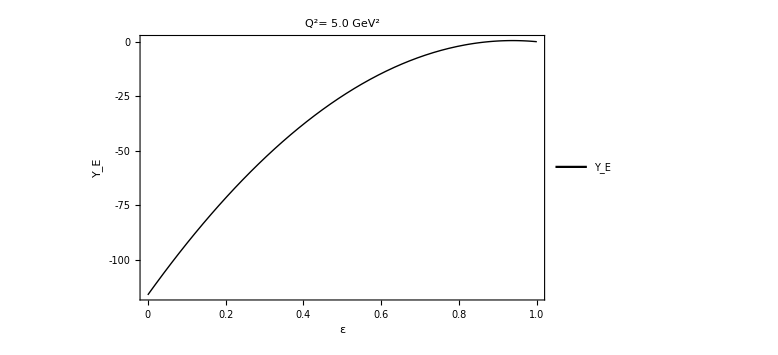

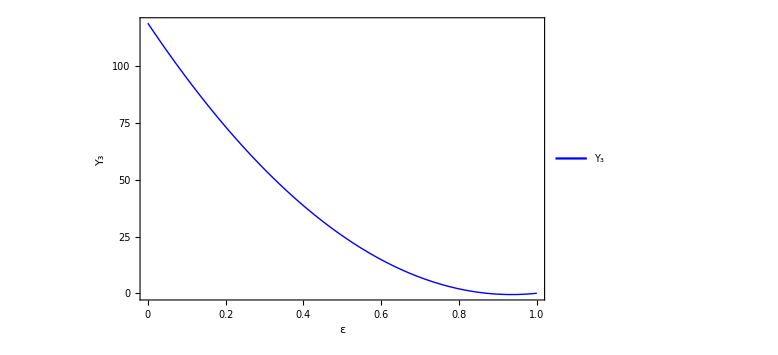

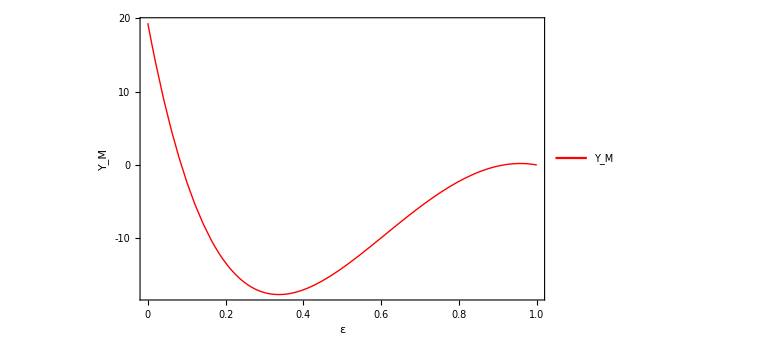

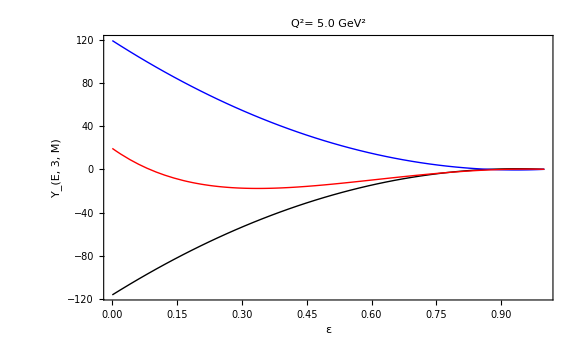

```mathematica
YEplotfc=Plot[YEfc, {eps,0,1},PlotStyle->{Black,Thick},FrameLabel->{Style["ε",Bold,16],Style["Y_E",Bold,16]},PlotLegends-> Placed[LineLegend[{"Y_E"},LabelStyle->Directive[22]],{0.9,0.8}], Frame-> True,FrameTicks->All,PlotLabel->Style["Q^2= 5.0 GeV^2",Bold,24], ImageSize-> Large]
Y3plotfc=Plot[Y3fc, {eps,0,1},PlotStyle->{Blue,Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_3",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_3"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]
YMplotfc=Plot[YMfc, {eps,0,1},PlotStyle->{Red, Thick},FrameLabel->{Style["ε",Bold,18],Style["Y_M",Bold,18]},PlotLegends-> Placed[LineLegend[{"Y_M"},LabelStyle->Directive[22]],{0.9,0.8}],Frame-> True,FrameTicks->All,ImageSize-> Large]

Show[YEplotfc,Y3plotfc,YMplotfc,PlotRange->All,FrameLabel->{Style["ε",Bold,26],Style["Y_(E, 3, M)  ",Bold,24]},Frame-> True,FrameTicks->All,FrameTicksStyle-> Directive[Black,14],ImageSize-> Large]
```